```mathematica
U[dx_,dt_] := Normal[Series[u[dx h z+x,dt k z+t],{z,0,4}]]/.{z->1}
```

```mathematica
LTE=FullSimplify[1/(2k)(U[0,2]-U[0,0])-1/h^2(U[-1,1]-2U[0,1]+U[1,1]),Assumptions->{D[u[x,t],t]==D[u[x,t],{x,2}],D[u[x,t],{t,2}]==D[u[x,t],t,{x,2}],D[u[x,t],{t,3}]==D[u[x,t],{x,2},{t,2}]}]
(* find a better way to add assumptons *)
```

1/6 k^2 (2 k u^(0,4)[x,t]+u^(2,2)[x,t])-1/12 h^2 u^(4,0)[x,t]

### Problem 2

```mathematica
U[dx_,dt_] := Normal[Series[u[dx h z+x,dt k z+t],{z,0,4}]]/.{z->1}
```

```mathematica
LTE=Collect[FullSimplify[1/k(U[0,1]-U[0,0])-κ/(2 h^2)(U[-1,0]-2U[0,0]+U[1,0]+U[-1,1]-2U[0,1]+U[1,1])+ γ((1-θ)U[0,0]+θ U[0,1]),Assumptions->{D[u[x,t],t]==κ D[u[x,t],{x,2}]-γ u[x,t],D[u[x,t],{t,2}]==κ D[u[x,t],t,{x,2}]-γ D[u[x,t],t]}
],{k,h},Simplify]
```

1/24 k^4 γ θ u^(0,4)[x,t]+1/24 k^3 (4 γ θ u^(0,3)[x,t]+u^(0,4)[x,t])-1/2 k (-1+2 θ) (u^(0,2)[x,t]-κ u^(2,1)[x,t])+1/12 k^2 (6 γ θ u^(0,2)[x,t]+2 u^(0,3)[x,t]-3 κ u^(2,2)[x,t])-1/12 h^2 κ u^(4,0)[x,t]

```mathematica
Normal[Series[f[a z+x,b z+y],{z,0,2}]]/.{z->1}
```

f[x,y]+b f^(0,1)[x,y]+a f^(1,0)[x,y]+1/2 (b^2 f^(0,2)[x,y]+2 a b f^(1,1)[x,y]+a^2 f^(2,0)[x,y])

```mathematica
Normal[Series[f[x+a z],{z,0,2}]]/.{z->1}
```

f[x]+a f'[x]+1/2 a^2 f''[x]

```mathematica
Normal[Series[Sqrt[a z+1],{z,0,4}]]/.{z->1}
```

1+a/2-a^2/8+a^3/16-(5 a^4)/128

```mathematica
FullSimplify[y-√(y^2+1)<-1,Assumptions->{y<0}]
```

True

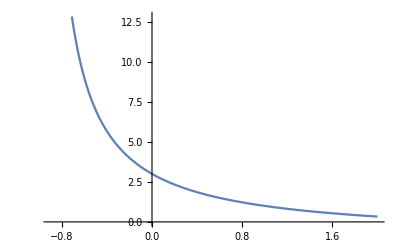

```mathematica
Plot[{(1-z+2)/(1+z)},{z,-.9,2}]
```